NIntegrate::nlim: z = s is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

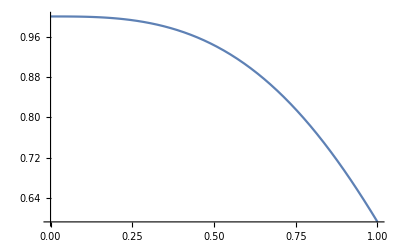

```mathematica
u[s_]:=Exp[NIntegrate[Exp[z^2],{z,0,s}]];
x[t_]:=1/u[t]+(1/u[t]) NIntegrate[u[s] Cos[s],{s,0,t}];
Plot[x[t],{t,0,1}]
```

NIntegrate::nlim: s = s$3339146 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

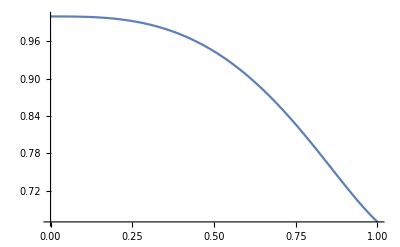

```mathematica
Clear[x,t,s];
x[1,t_]:=1+NIntegrate[-Exp[s^2]+Cos[s],{s,0,t}];
x[2,t_]:=1+Module[{s},NIntegrate[-Exp[s^2]*x[1,s]+Cos[s],{s,0,t}]];
Plot[x[2,t],{t,0,1}]
```

NIntegrate::nlim: s = s$5290225 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

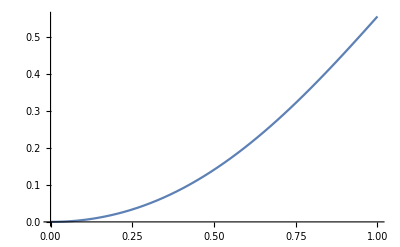

```mathematica
Clear[x,t,s];
x[1,t_]:=0+NIntegrate[Sin[0+s],{s,0,t}];
x[2,t_]:=0+Module[{s},NIntegrate[Sin[x[1,s]+s],{s,0,t}]];
w=NDSolve[{y'[t]==Sin[y[t]+t],y[0]==0},y,{t,0,1}];
Plot[x[2,t],{t,0,1}]
```

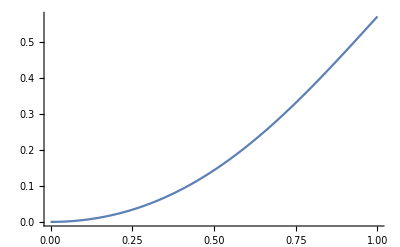

```mathematica
Plot[Evaluate[y[t]/.w],{t,0,1},PlotRange->All]
```

NIntegrate::nlim: s = s$6443808 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

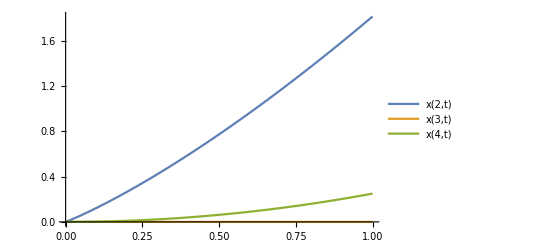

```mathematica
Clear[x,t,s]
x[1,t_]:=t+NIntegrate[Sqrt[s],{s,0,t}];
x[2,t_]:=t+Module[{s},NIntegrate[Sqrt[x[1,s]],{s,0,t}]];
x[3,t_]:=0;
x[4,t_]:=t^2/4;
Plot[{x[2,t],x[3,t],x[4,t]},{t,0,1},PlotLegends->"Expressions"]
```